# Calculating G0ΣG0 (p, τ) for BEC Polaron

## Parameters and Equations

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx
```

## Integrating τ1 and τ2

```mathematica
foig[p_,q_,τ_,τ1_, τ2_] := 4*Pi/(2*Pi)^3*q^2*g0[p,tbeg, τ1]*g0[p-q,τ1,τ2]*dq[q,τ1,τ2]*vq2[q]*g0[p,τ2,τ];
```

### Try to do everything at once qith NIntegrate

```mathematica
fo[p_,τ_]:=NIntegrate[foig[p,q,τ,τ1,τ2],{τ1,0,τ2},  {τ2,0,τ},{q,-qc,qc}];
LogPlot[fo[0,τ],{τ,1,2},PlotPoints->10,MaxRecursion->1,PlotRange->Full]
```

-Graphics-

### Plot of final Integrand for q Integral

```mathematica
f[p_,q_,τ_,τ2_]:=Integrate[foig[p,q,τ,τ1,τ2],  {τ1,0,τ2}]
```

```mathematica
g[p_,q_,τ_]:=Integrate[f[p,q,τ,τ2],{τ2,0,τ}]
```

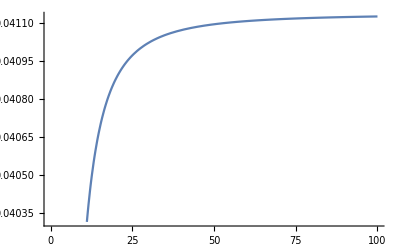

```mathematica
Plot[g[0,q,1],{q,0,100}]
```

## Q Integral

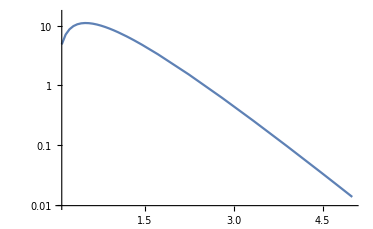

```mathematica
LogPlot[NIntegrate[g[0,q,τ],{q,0,qc}],{τ,0.1,5}, PlotPoints->10, MaxRecursion->3, PlotRange->Full]
```

```mathematica
data = Table[{τ, NIntegrate[g[0,q,τ],{q,0,qc}, MinRecursion->5]},{τ, 0.1, 8, 0.02}];
```

```mathematica
DumpSave["G0SEG0.mx", data];
Export["mat_fo_g0seg0", data, "Table"];
```

## Laplace Transform to Σ1 (p=0, ω)

```mathematica
<<1st_SEw.mx;
```

```mathematica
Laplacedata = Table[{ω, NIntegrate[g[0,q,τ]* Exp[ω*τ]/g0pw[0,ω,0]^2,{τ,0,Infinity}, {q,0,qc}]},{ω, -100, 0, 1}];
```

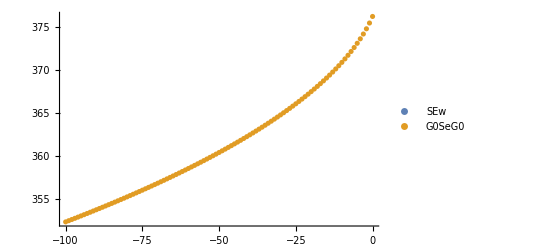

```mathematica
LaplacePlot =ListPlot[{Σomegadata,Laplacedata}, PlotLegends->{"SEw","G0SeG0" }]
```